```mathematica
SetDirectory[NotebookDirectory[]]
SAMPLE["2j"]= Import["process1_dijet.out", "Table"];
SAMPLE["Wj"]= Import["process2_Wjet.out", "Table"];
SAMPLE["Zj"]= Import["process3_Zjet.out", "Table"];
SAMPLE["Hj"]= Import["process4_Hjet.out", "Table"];
SAMPLE["γj"]= Import["process5_gammajet.out", "Table"];
```

/Users/jthaler/Dropbox (MIT)/QuarkGluon/PythiaStudies

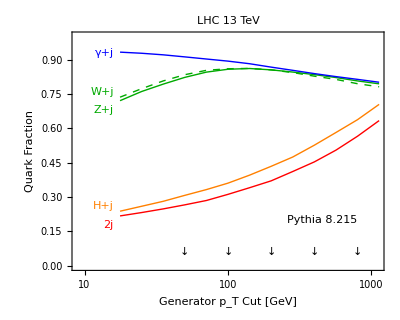

fig_parton_level_qg_composition.pdf

```mathematica
STYLE["2j"] = Directive[Thickness[Medium], Red];
STYLE["Wj"] = Directive[Thickness[Medium], Dashed, Darker[Green]];
STYLE["Zj"] = Directive[Thickness[Medium], Darker[Green]];
STYLE["Hj"] = Directive[Thickness[Medium], Orange];
STYLE["γj"] = Directive[Thickness[Medium], Blue];

smalltick = 0.010;
largetick = 0.020;

MYTICKS ={ 
{Identity[10], "10", {largetick,0}},
{Identity[20], "20", {smalltick,0}},
{Identity[30], "", {smalltick,0}},
{Identity[40], "", {smalltick,0}},
{Identity[50], "50", {smalltick,0}},
{Identity[60], "", {smalltick,0}},
{Identity[70], "", {smalltick,0}},
{Identity[80], "", {smalltick,0}},
{Identity[90], "", {smalltick,0}},
{Identity[100], "100", {largetick,0}},
{Identity[200], "200", {smalltick,0}},
{Identity[300], "", {smalltick,0}},
{Identity[400], "", {smalltick,0}},
{Identity[500], "500", {smalltick,0}},
{Identity[600], "", {smalltick,0}},
{Identity[700], "", {smalltick,0}},
{Identity[800], "", {smalltick,0}},
{Identity[900], "", {smalltick,0}},
{Identity[1000], "1000", {largetick,0}}
};

MYSILENTTICKS ={ 
{Identity[10], "", {largetick,0}},
{Identity[20], "", {smalltick,0}},
{Identity[30], "", {smalltick,0}},
{Identity[40], "", {smalltick,0}},
{Identity[50], "", {smalltick,0}},
{Identity[60], "", {smalltick,0}},
{Identity[70], "", {smalltick,0}},
{Identity[80], "", {smalltick,0}},
{Identity[90], "", {smalltick,0}},
{Identity[100], "", {largetick,0}},
{Identity[200], "", {smalltick,0}},
{Identity[300], "", {smalltick,0}},
{Identity[400], "", {smalltick,0}},
{Identity[500], "", {smalltick,0}},
{Identity[600], "", {smalltick,0}},
{Identity[700], "", {smalltick,0}},
{Identity[800], "", {smalltick,0}},
{Identity[900], "", {smalltick,0}},
{Identity[1000], "", {largetick,0}}
};

MYPLOT = ListLogLinearPlot[{SAMPLE["2j"],SAMPLE["Wj"],SAMPLE["Zj"],SAMPLE["Hj"],SAMPLE["γj"]}, Joined-> True, PlotRange-> {{10*0.9, 1000/0.9},{0,1}}, Frame ->True, BaseStyle -> {FontFamily->"Times",14}, FrameStyle -> Thickness[Medium], PlotTheme-> "Classic", LabelStyle ->  {FontFamily->"Times", Black}, FrameLabel-> {"Generator p_T Cut [GeV]","Quark Fraction"}, PlotLabel -> "LHC 13 TeV", PlotStyle -> {STYLE["2j"],STYLE["Wj"],STYLE["Zj"],STYLE["Hj"],STYLE["γj"]}, AspectRatio -> 0.8,FrameTicks -> {{Automatic,Automatic},{MYTICKS,MYSILENTTICKS}}];
MYOVERLAY=  ListLogLinearPlot[{{#, 0.06}&/@{50,100,200,400,800}}, Joined -> False, PlotRange-> {{10*0.9, 1000/0.9},{0,1}}, Frame ->True, BaseStyle -> {FontFamily->"Times",14}, FrameStyle -> Thickness[Medium], PlotTheme-> "Classic", LabelStyle ->  {FontFamily->"Times", Black}, FrameLabel-> {"Generator p_T Cut [GeV]","Quark Fraction"}, PlotLabel -> "LHC 13 TeV", PlotStyle -> {Black}, AspectRatio -> 0.8, PlotMarkers -> {"↓"}, FrameTicks -> {{Automatic,Automatic},{MYTICKS,MYSILENTTICKS}}];
Show[MYOVERLAY,MYPLOT,Graphics[{STYLE["2j"] ,Text["2j",{Log[16],0.18},{1,0}],
STYLE["Wj"] ,Text["W+j",{Log[16],0.76},{1,0}],
STYLE["Zj"] ,Text["Z+j",{Log[16],0.68},{1,0}],
STYLE["Hj"] ,Text["H+j",{Log[16],0.26},{1,0}],
STYLE["γj"] ,Text["γ+j",{Log[16],0.93},{1,0}],
Black, Text[Style["Pythia 8.215",Italic],{Log[800],0.2},{1,0}]
}]]
Export["fig_parton_level_qg_composition.pdf",%]
```